```mathematica
LeafShrinking[graph_]:=Module[{G=graph,pos,deg2,leaf,neighbors},
While[Length[VertexList[G]]>2,
If[MemberQ[VertexDegree[G],1],
pos=Position[VertexDegree[G],1];
leaf=VertexList[G][[pos[[1]]]];
G=VertexDelete[G,leaf],

If[MemberQ[VertexDegree[G],2],
pos=Position[VertexDegree[G],2];
deg2=VertexList[G][[pos[[1]]]];
neighbors=AdjacencyList[G,deg2];
If[Not[MemberQ[AdjacencyList[G,neighbors[[1]]],neighbors[[2]]]],
G=EdgeAdd[VertexDelete[G,deg2],neighbors[[1]]<->neighbors[[2]]],G=VertexDelete[G,deg2]],


Return[G];


]





]];Return[G]];




EdgebasedQ[graph_]:=Module[{},If[Length[VertexList[LeafShrinking[graph]]]==2,Return[True],Return[False]]];


LeafCutting[graph_]:=Module[{G=graph,pos,leaflist,i},

If[MemberQ[VertexDegree[G],1],
pos=Flatten[Position[VertexDegree[G],1]];
leaflist=VertexList[G][[pos]]];

For[i=1,i≤Length[leaflist],i++,G=VertexDelete[G,leaflist[[i]]];];


Return[G];


];



LeafAttachmentPoints[graph_]:=Module[{vertices,degrees,returnlist,pos,i,currentleaf},
vertices=VertexList[graph];
degrees=VertexDegree[graph];
returnlist={};
If[MemberQ[degrees,1],
pos=Position[degrees,1];
For[i=1,i≤Length[pos],i++,
currentleaf=vertices[[pos[[i]]]];
returnlist=Join[returnlist,AdjacencyList[graph,currentleaf]];




];


];Return[DeleteDuplicates[returnlist]];];





(*TreebasedQ[graph_]:= (*Gives correct answer if there are at most two leaves. With more than 2 leaves, if this function says "True", then the network IS treebased. However, if the answer is "False", the answer is not guaranteed to be correct. In short: Only a Hamiltonian path between two leaf attachment points is sought for. If this exists, the network must be treebased, but if it doesn't, this only implies non-treebasedness in the case where the network only has two leaves.
*)Module[{currentg,leafneighbors,neighborpairs,hamilton,counter,currentpair,newgraph,hamiltonlist,j,hamilgraph},
If[Not[ProperQ[graph]],Return[False]];
If[EdgebasedQ[graph],Return[True]];
If[Length[VertexList[graph]]==1,Return[True]];

currentg=LeafCutting[graph];
leafneighbors=LeafAttachmentPoints[graph];
neighborpairs=Subsets[leafneighbors,{2}];


hamilton=False;counter=1;


While[hamilton==False&&counter<=Length[neighborpairs],
currentpair=neighborpairs[[counter]];

If[Not[MemberQ[AdjacencyList[currentg,currentpair[[1]]],currentpair[[2]]]],newgraph=EdgeAdd[currentg,currentpair[[1]]<->currentpair[[2]]],newgraph=currentg];

hamiltonlist=FindHamiltonianCycle[newgraph,All];


For[j=1,j≤Length[hamiltonlist],j++,

hamilgraph=Graph[hamiltonlist[[j]]];

If[MemberQ[AdjacencyList[hamilgraph,currentpair[[1]]],currentpair[[2]]],
hamilton=True;Break[];];

];
counter++;
];
Return[hamilton];

];*)


IsTreeQ[graph_]:=Module[{},If[ConnectedGraphQ[graph]&&Length[EdgeList[graph]]==Length[VertexList[graph]]-1,Return[True],Return[False]]];



Levelkblob[blob_]:=(*CAREFUL!!! WORKS ONLY FOR A SIMPLE NETWORK WITH ONLY ONE BLOB (with or without leaves)! OTHERWISE, ALL BLOBS WILL BE ADDED UP!*)

Module[{numberofnodes=Length[VertexList[blob]],i,delete,j,k,kmax,currentgraph,edges=EdgeList[blob],deleteedges},

If[IsTreeQ[blob],Return[0]];

kmax=Length[edges]-(numberofnodes-1);

For[k=1,k≤kmax,k++,
deleteedges=Subsets[edges,{k}];

For[j=1,j≤Length[deleteedges],j++,
delete=deleteedges[[j]];

currentgraph=blob;
For[i=1,i≤Length[delete],i++,
currentgraph=EdgeDelete[currentgraph,delete[[i]]];
];

If[IsTreeQ[currentgraph],Return[k]];


];

];]



Levelk[conngraph_]:=Module[{edges=EdgeList[conngraph],comp,currentvertices,currentgraph,j,nodes=VertexList[conngraph],levellist,graph=conngraph,i,cutedges={}},

For[i=1,i≤Length[edges],i++,
If[Not[ConnectedGraphQ[EdgeDelete[graph,edges[[i]]]]],AppendTo[cutedges,edges[[i]]];]

];


For[i=1,i≤Length[cutedges],i++,

graph=EdgeDelete[graph,cutedges[[i]]];
];


comp=ConnectedComponents[graph];levellist={};

For[i=1,i≤Length[comp],i++, 
currentvertices=comp[[i]];
currentgraph=graph;
For[j=1,j≤Length[nodes],j++,
If[Not[MemberQ[currentvertices,nodes[[j]]]],currentgraph=VertexDelete[currentgraph,nodes[[j]]]]];



AppendTo[levellist,Levelkblob[currentgraph]];];

Return[Max[levellist]];



]



ProperQ[g_]:=Module[{cutedge,cutvertex,edges=EdgeList[g],vertices=VertexList[g],i,newgraph,j,components,k,currentedges,currentnodes,relevantedges,currentcomp},
If[Not[ConnectedGraphQ[g]],Return[False]];
If[Length[VertexList[g]]==1,Return[True]];
If[Count[VertexDegree[g],1]+Count[VertexDegree[g],0]==0,Return[False]];
If[Count[VertexDegree[g],2]≠0,Return[False]];

If[EdgeConnectivity[g]>1,cutedge=False,cutedge=True];
If[VertexConnectivity[g]>1,cutvertex=False,cutvertex=True];

If[Not[cutedge]&&Not[cutvertex],Return[True]];

If[cutedge,
For[i=1,i≤Length[edges],i++, newgraph=EdgeDelete[g,edges[[i]]];currentedges=EdgeList[newgraph];

If[Not[ConnectedGraphQ[newgraph]],components=ConnectedComponents[newgraph];
For[j=1,j≤Length[components],j++,

currentnodes=components[[j]];
relevantedges={};

For[k=1,k≤Length[currentedges],k++,
If[MemberQ[currentnodes,currentedges[[k]][[1]]]&&MemberQ[currentnodes,currentedges[[k]][[2]]],AppendTo[relevantedges,currentedges[[k]]]];

];

currentcomp=Graph[components[[j]],relevantedges];


If[Count[VertexDegree[currentcomp],1]+Count[VertexDegree[currentcomp],0]==0,Return[False]];

];


];
];
];

If[Not[cutvertex],Return[True]];

If[cutvertex,For[i=1,i≤Length[vertices],i++,newgraph=VertexDelete[g,vertices[[i]]];

If[Not[ConnectedGraphQ[newgraph]],components=ConnectedComponents[newgraph];
For[j=1,j≤Length[components],j++,

currentnodes=components[[j]];
relevantedges={};

For[k=1,k≤Length[currentedges],k++,
If[MemberQ[currentnodes,currentedges[[k]][[1]]]&&MemberQ[currentnodes,currentedges[[k]][[2]]],AppendTo[relevantedges,currentedges[[k]]]];

];

currentcomp=Graph[components[[j]],relevantedges];

If[Count[VertexDegree[currentcomp],1]+Count[VertexDegree[currentcomp],0]==0,Return[False]];

];

];

];

Return[True];
];
]

SuppressDeg2Nodes[graph_]:=Module[{G=graph,pos,deg2,leaf,neighbors},
While[Length[VertexList[G]]>2,

If[MemberQ[VertexDegree[G],2],
pos=Position[VertexDegree[G],2];
deg2=VertexList[G][[pos[[1]]]];
neighbors=AdjacencyList[G,deg2];
If[Not[MemberQ[AdjacencyList[G,neighbors[[1]]],neighbors[[2]]]],
G=EdgeAdd[VertexDelete[G,deg2],neighbors[[1]]<->neighbors[[2]]],G=VertexDelete[G,deg2]],


Return[G];


];





];Return[G]];






IndependentTriangles[graph_]:=Module[{independentTriangles={},triangles={},vertices=VertexList[graph],edges=EdgeList[graph],vertexnumber,i,j,k,neighbors,currentvertex,int,currenttriangle,neighbors1,neighbors2,neighbors3},

vertexnumber=Length[vertices];

For[i=1,i≤vertexnumber,i++,
currentvertex=vertices[[i]];
neighbors=AdjacencyList[graph,currentvertex];

For[j=1,j≤Length[neighbors],j++,
int=Intersection[neighbors,AdjacencyList[graph,neighbors[[j]]]];
If[int≠ {},
For[k=1,k≤Length[int],k++,
AppendTo[triangles,Sort[{currentvertex,neighbors[[j]],int[[k]]}]]];


]


];
];

triangles=DeleteDuplicates[triangles];



For[i=1,i≤Length[triangles],i++,
currenttriangle=triangles[[i]];

neighbors1=AdjacencyList[graph,currenttriangle[[1]]];
neighbors1=Delete[neighbors1,Position[neighbors1,currenttriangle[[2]]]];
neighbors1=Delete[neighbors1,Position[neighbors1,currenttriangle[[3]]]];

neighbors2=AdjacencyList[graph,currenttriangle[[2]]];
neighbors2=Delete[neighbors2,Position[neighbors2,currenttriangle[[1]]]];
neighbors2=Delete[neighbors2,Position[neighbors2,currenttriangle[[3]]]];


neighbors3=AdjacencyList[graph,currenttriangle[[3]]];
neighbors3=Delete[neighbors3,Position[neighbors3,currenttriangle[[1]]]];
neighbors3=Delete[neighbors3,Position[neighbors3,currenttriangle[[2]]]];


If[Intersection[neighbors1,neighbors2]=={}&&Intersection[neighbors2,neighbors3]=={}&&Intersection[neighbors1,neighbors3]=={},AppendTo[independentTriangles,currenttriangle];]; 






];Return[independentTriangles];]


TriangleReduction[graph_,triangles_]:=Module[{},Return[graph]];



(*TriangleReduction[graph_,triangles_]:=Module[{vertices,edges=EdgeList[graph],vertexnumber,i,currentgraph=graph,currenttriangle,numberoftriangles=Length[triangles],newnode,j,neighbors,neighbors1,neighbors2,neighbors3},
vertexnumber=Length[vertices];


For[i=1,i≤numberoftriangles,i++,
currenttriangle=triangles[[i]];
newnode=StringJoin[currenttriangle[[1]],currenttriangle[[2]],currenttriangle[[3]]];

vertices=VertexList[currentgraph];
edges=EdgeList[currentgraph];


neighbors1=AdjacencyList[currentgraph,currenttriangle[[1]]];
neighbors1=Delete[neighbors1,Position[neighbors1,currenttriangle[[2]]]];
neighbors1=Delete[neighbors1,Position[neighbors1,currenttriangle[[3]]]];

neighbors2=AdjacencyList[currentgraph,currenttriangle[[2]]];
neighbors2=Delete[neighbors2,Position[neighbors2,currenttriangle[[1]]]];
neighbors2=Delete[neighbors2,Position[neighbors2,currenttriangle[[3]]]];


neighbors3=AdjacencyList[currentgraph,currenttriangle[[3]]];
neighbors3=Delete[neighbors3,Position[neighbors3,currenttriangle[[1]]]];
neighbors3=Delete[neighbors3,Position[neighbors3,currenttriangle[[2]]]];

neighbors=Sort[Join[neighbors1,neighbors2,neighbors3]];

AppendTo[vertices,newnode];



For[j=1,j≤Length[neighbors],j++,
If[Not[MemberQ[edges,newnode<->neighbors[[j]]]]&&Not[MemberQ[edges,neighbors[[j]]<->newnode]],
AppendTo[edges,newnode<->neighbors[[j]]]];
];

currentgraph=VertexDelete[Graph[vertices,edges,VertexLabels->"Name"],currenttriangle];




];
Return[currentgraph];
];*)



getCore[graph_]:=Module[{vertexnumber=VertexCount[graph],lsgraph,triangleredgraph},

lsgraph=LeafShrinking[graph];
triangleredgraph=TriangleReduction[lsgraph,IndependentTriangles[lsgraph]];

While[VertexCount[lsgraph]!=VertexCount[triangleredgraph],
lsgraph=LeafShrinking[triangleredgraph];
triangleredgraph=TriangleReduction[lsgraph,IndependentTriangles[lsgraph]];
];

Return[triangleredgraph]




];



getExtendedCore[graph_]:=Module[{core=getCore[graph],relevantedges={},graphEdges,coreEdges,noOfCoreEdges,currentedge,currentvertices,vertex1,vertex2,path,extcoreedges,extcorevertices,coreVertices,forbiddennodes,edgereplacementlist={},i},
graphEdges=EdgeList[graph];
coreEdges=EdgeList[core];
noOfCoreEdges=Length[coreEdges];
coreVertices=VertexList[core];

For[i=1,i≤noOfCoreEdges,i++,
currentedge=coreEdges[[i]];
If[Not[MemberQ[graphEdges,currentedge]],AppendTo[relevantedges,currentedge]];


];

extcoreedges=coreEdges;extcorevertices=coreVertices;

For[i=1,i≤Length[relevantedges],i++,
currentedge=relevantedges[[i]];
currentvertices=VertexList[Graph[{currentedge}]];
vertex1=currentvertices[[1]];
vertex2=currentvertices[[2]];
forbiddennodes=Delete[coreVertices,Position[coreVertices,vertex1]];
forbiddennodes=Delete[forbiddennodes,Position[forbiddennodes,vertex2]];

path=FindShortestPath[VertexDelete[graph,forbiddennodes],vertex1,vertex2];

extcorevertices=Flatten[AppendTo[extcorevertices,path]];

AppendTo[edgereplacementlist,{currentedge,path}];


];

Return[{Subgraph[graph,extcorevertices,VertexLabels->"Name"],edgereplacementlist,core}]


];






findSpecialnodes[graph_]:=Module[{specialnodes={},extcore,vertices,i,vertexcount,extoutput},

extoutput=getExtendedCore[graph];
extcore=extoutput[[1]];
vertices=VertexList[extcore];
vertexcount=Length[vertices];


For[i=1,i≤vertexcount,i++,


If[VertexDegree[extcore,vertices[[i]]]≠VertexDegree[graph,vertices[[i]]],AppendTo[specialnodes,vertices[[i]]]];

];
Return[{specialnodes,extoutput}];

];





NumberOfPathExits[graph_,path_]:=Module[{i,pathvertices,othervertices,newgraph,relevantcomponents,leftovernodes,leaf,neighbor},
If[Length[path]==2,Return[0],
If[Length[path]==3,Return[1],

(*Figure out if there are at least two independent leaves by checking if there are two independent paths from one edgepath vertex to a fixed leaf's neighbor*)

(*First we need to find the leaves in the relevant components*)

pathvertices=path;
pathvertices=Delete[pathvertices,Position[pathvertices,path[[1]]]];
pathvertices=Delete[pathvertices,Position[pathvertices,path[[Length[path]]]]];
othervertices=Complement[VertexList[graph],pathvertices];
newgraph=Subgraph[graph,othervertices,VertexLabels->"Name"];


relevantcomponents=Complement[ConnectedComponents[newgraph],ConnectedComponents[newgraph,{path[[1]],path[[Length[path]]]}]
];



If[Length[relevantcomponents>1],Return[2]];
leftovernodes=VertexList[Subgraph[graph,relevantcomponents[[1]]]];

leaf=" ";
For[i=1,i≤Length[leftovernodes],i++,
If[VertexDegree[graph,leftovernodes[[i]]]==1,leaf=leftovernodes[[i]];Break[]];


];


neighbor=AdjacencyList[graph,leaf][[1]];

newgraph=Subgraph[graph,Join[VertexList[newgraph],{path[[2]]}],VertexLabels->"Name"];

Return[Min[2,Length[FindVertexIndependentPaths[newgraph,path[[2]],neighbor,2]]]];





]

]



]







TreePruning[graph_]:=Module[{newgraph=graph,vertices,i,currentvertex,comp,j,leaves,delete},
vertices=VertexList[newgraph];


For[i=1,i<=Length[vertices],i++,

currentvertex=vertices[[i]];
comp=ConnectedComponents[VertexDelete[graph,currentvertex]];

(*replace all tree components with single leaves*)


For[j=1,j≤Length[comp],j++,
If[IsTreeQ[Subgraph[newgraph,comp[[j]]]],newgraph=VertexContract[newgraph,VertexList[Subgraph[newgraph,comp[[j]],VertexLabels->"Name"]]]];



];


];
(*If multiple leaves are attached to one node, delete all but one of them*)


vertices=VertexList[newgraph];leaves={};
For[i=1,i<=Length[vertices],i++,
If[VertexDegree[newgraph,vertices[[i]]]==1,AppendTo[leaves,vertices[[i]]]];
];


delete={};

For[i=1,i≤Length[leaves]-1,i++,
For[j=i+1,j≤Length[leaves],j++,
If[AdjacencyList[newgraph,leaves[[i]]]==AdjacencyList[newgraph,leaves[[j]]],AppendTo[delete,leaves[[j]]]];
];
];


If[delete≠{},newgraph=VertexDelete[newgraph,DeleteDuplicates[delete]]];

Return[Graph[VertexList[newgraph],EdgeList[newgraph],VertexLabels->"Name"]];
];



NumberOfExitPaths[graph_,path_]:=Module[{newpath,newgraph,conn,wrongcomp,prunedgraph,counter,list,i},newpath=Delete[Delete[path,{Length[path]}],{1}];
newgraph=VertexDelete[graph,newpath];
conn=ConnectedComponents[newgraph];
wrongcomp=VertexComponent[newgraph,{path[[1]],path[[Length[path]]]}];
newgraph=VertexDelete[newgraph,wrongcomp];

counter=0;list=VertexList[newgraph];
For[i=1,i≤Length[list],i++,
If[VertexDegree[graph,list[[i]]]==1,counter++];

];

If[counter>=2,Return[2],Return[1]];





];





getKernel[graph_]:=Module[{specialoutput,currentgraph,specialnodes,corenodes,edgereplacement,noOfspecialnodes,i,j,newstring,vertices,edges,noOfedges,k,currentedgepath,currentpathlength,vertex1,vertex2,vertex1special,vertex2special,adjlisti,adjlistj,union,intersection,nonint,availableleaves,s},


specialoutput=findSpecialnodes[TreePruning[graph]];
currentgraph=specialoutput[[2]][[1]];
vertices=VertexList[currentgraph];
edges=EdgeList[currentgraph];

specialnodes=specialoutput[[1]];
corenodes=VertexList[specialoutput[[2]][[3]]];


For[i=1,i≤Length[corenodes],i++,
If[MemberQ[specialnodes,corenodes[[i]]],
newstring=StringJoin["coreleaf"(*core leaf*),ToString[i]];
AppendTo[vertices,newstring];
AppendTo[edges,newstring<->corenodes[[i]]]
(*specialnodes=Delete[specialnodes,Position[specialnodes,corenodes[[i]]]];*)

];
];




edgereplacement=specialoutput[[2]][[2]];
noOfedges=Length[edgereplacement];


For[k=1,k≤noOfedges,k++,
currentedgepath=edgereplacement[[k]][[2]];
currentpathlength=Length[currentedgepath]-2;
vertex1=currentedgepath[[1]];
vertex2=currentedgepath[[Length[currentedgepath]]];
vertex1special=MemberQ[specialnodes,vertex1];
vertex2special=MemberQ[specialnodes,vertex2];


If[Not[vertex1special&&vertex2special],
If[vertex1special||vertex2special||currentpathlength==1,
newstring=StringJoin[currentedgepath[[2]],"leaf",ToString[k]];
AppendTo[vertices,newstring];
AppendTo[edges,newstring<->currentedgepath[[2]]];

,

availableleaves=NumberOfExitPaths[TreePruning[graph],currentedgepath];

For[i=2,i≤availableleaves+1,i++,
newstring=StringJoin["path",currentedgepath[[1]],currentedgepath[[Length[currentedgepath]]],"leaf",ToString[i-1]];
AppendTo[vertices,newstring];
AppendTo[edges,newstring<->currentedgepath[[i]]];

];



];


];
];


edges=DeleteDuplicates[edges];

Return[SuppressDeg2Nodes[Graph[vertices,edges,VertexLabels->"Name"]]];


];
```

```mathematica
getGeneralizedKirchhoffMatrix[simplegraph_]:=Module[{edgeset,vertexset,matrix,node1,node2,i,j,rowsums},
edgeset=EdgeList[simplegraph];
vertexset=VertexList[simplegraph];
matrix=Table[0,{i,1,Length[vertexset]},{j,1,Length[vertexset]}];

For[i=1,i≤Length[vertexset]-1,i++,
For[j=i+1,j≤Length[vertexset],j++,

node1=vertexset[[i]];
node2=vertexset[[j]];

If[MemberQ[AdjacencyList[simplegraph,node1],node2],matrix[[i]][[j]]=StringJoin["e_",ToString[node1],"-",ToString[node2]];matrix[[j]][[i]]=matrix[[i]][[j]]];


];];

rowsums=Table[0,{i,1,Length[vertexset]}];
For[i=1,i≤Length[vertexset],i++,
For[j=1,j≤Length[vertexset],j++,
rowsums[[i]]=rowsums[[i]]+matrix[[i]][[j]];


]

];

For[i=1,i≤Length[vertexset],i++,
matrix[[i]][[i]]=-rowsums[[i]];
];

Return[matrix];








]
getKirchhoffPolynomial[simplegraph_]:=Module[{mat,n,matnew},mat=getGeneralizedKirchhoffMatrix[simplegraph];
n=Length[mat];
matnew=Delete[mat,Length[mat]];
matnew=Transpose[matnew];
matnew=Delete[matnew,Length[matnew]];
matnew=Transpose[matnew];
Return[ExpandAll[Det[matnew]]];


];



getAllSpanningTrees[simplegraph_]:=Module[{treelist,spanningtrees,i},
treelist=StringSplit[ToString[getKirchhoffPolynomial[getKernel[simplegraph]]],"+"];
For[i=1,i≤Length[treelist],i++,
treelist[[i]]=StringDelete[treelist[[i]],"e_"];
treelist[[i]]=StringReplace[treelist[[i]]," "->","];
If[i>1,treelist[[i]]=StringDrop[treelist[[i]],1]];
If[i<Length[treelist],treelist[[i]]=StringDrop[treelist[[i]],-1]];
treelist[[i]]=StringReplace[treelist[[i]],"-"->"<->"];

treelist[[i]]=ToExpression[StringSplit[treelist[[i]],","]];

];

spanningtrees={};
For[i=1,i≤Length[treelist],i++,
AppendTo[spanningtrees,Graph[treelist[[i]],VertexLabels->"Name"]];


];

Return[spanningtrees];




];



getAllSupportTrees[phylonetwork_]:=Module[{spanningtrees,i,supporttrees,leafnumber},spanningtrees=getAllSpanningTrees[phylonetwork];
supporttrees={};
leafnumber=Count[VertexDegree[phylonetwork],1];

For[i=1,i≤Length[spanningtrees],i++,
If[Count[VertexDegree[spanningtrees[[i]]],1]==leafnumber,AppendTo[supporttrees,spanningtrees[[i]]]];



];
Return[{supporttrees,Length[supporttrees]}];


];




FindASupportTree[phylonetwork_]:=Module[{spanningtrees,i,supporttrees,leafnumber},spanningtrees=getAllSpanningTrees[phylonetwork];
supporttrees={};
leafnumber=Count[VertexDegree[phylonetwork],1];

For[i=1,i≤Length[spanningtrees],i++,
If[Count[VertexDegree[spanningtrees[[i]]],1]==leafnumber,AppendTo[supporttrees,spanningtrees[[i]]];Break[]];



];
Return[supporttrees];


];



ExtendedTreeBasedQ[phylonetwork_]:=(*Gives the correct answer in ALL cases, even with more than two leaves!*)Module[{supp=FindASupportTree[phylonetwork]},If[supp≠{},Print[Style["Your network is treebased!",FontColor->Red]];Print["This is a support tree: "];Print[supp[[1]]];Print["edge set of the support tree: ",EdgeList[supp[[1]]]];Return[True],Return[False]]];

TreeBasedQ[phylonetwork_]:=(*Gives the correct answer in ALL cases, even with more than two leaves!*)Module[{supp=FindASupportTree[phylonetwork]},If[supp≠{},Return[True],Return[False]]];
```

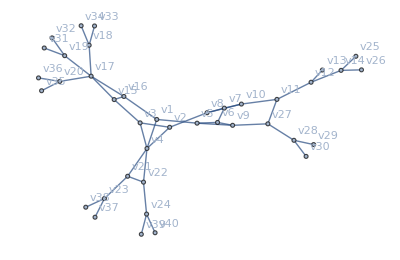

```mathematica
example=Graph[{"v1","v2","v3","v4","v5","v6","v7","v8","v9","v10","v11","v12","v13","v14","v15","v16","v17","v18","v19","v20","v21","v22","v23","v24"},{"v1"<->"v5","v1"<->"v4","v1"<->"v16","v2"<->"v3","v2"<->"v4","v2"<->"v8","v3"<->"v4","v3"<->"v15","v4"<->"v21","v4"<->"v22","v5"<->"v6","v5"<->"v9","v6"<->"v7","v6"<->"v9","v7"<->"v8","v7"<->"v10","v8"<->"v10","v10"<->"v11","v11"<->"v12","v12"<->"v13","v12"<->"v14","v15"<->"v16","v15"<->"v17","v16"<->"v17","v17"<->"v18","v17"<->"v19","v17"<->"v20","v21"<->"v22","v21"<->"v23","v22"<->"v24","v14"<->"v25","v14"<->"v26","v11"<->"v27","v27"<->"v9","v27"<->"v28","v28"<->"v29","v28"<->"v30","v19"<->"v31","v19"<->"v32","v18"<->"v33","v18"<->"v34","v20"<->"v35","v20"<->"v36","v23"<->"v37","v23"<->"v38","v24"<->"v39","v24"<->"v40"},VertexLabels->"Name"]
```

```mathematica
NumberOfExitPaths[example,{"v1","v5","v6","v7","v8","v2"}]
```

2

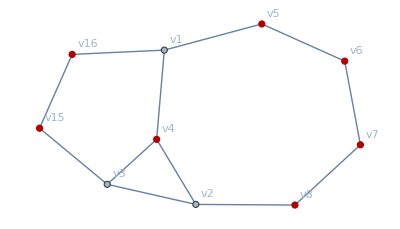

```mathematica
HighlightGraph[getExtendedCore[example][[1]],findSpecialnodes[example][[1]]]
```

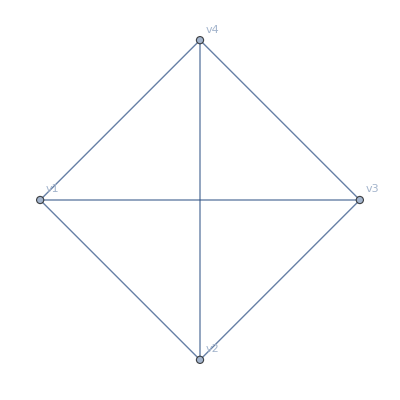

```mathematica
getCore[example]
```

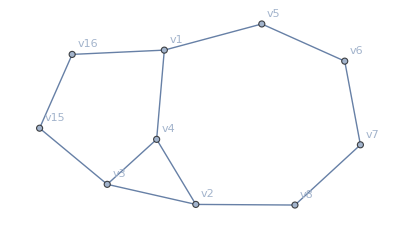

```mathematica
getExtendedCore[example][[1]]
```

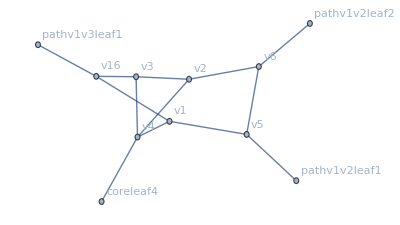

```mathematica
getKernel[example]
```

```mathematica
example
```

-Graphics-

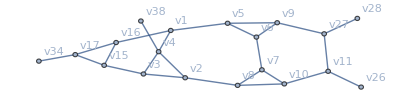

```mathematica
TreePruning[example]
```

```mathematica
getKernel[example]
```

-Graphics-

```mathematica
NumberOfExitPaths[TreePruning[example],{"v1","v5","v6","v7","v8","v2"}]
```

2